```mathematica
SetDirectory[NotebookDirectory[]];
```

## Data

```mathematica
localization=Import["Localization_sorted_12dockings_32nt.csv"];
```

## Using CDF Fitting to Fit the Data

## Plotting the CDF

```mathematica
yaxis=Range[0,1,1/Length[localization]];
```

```mathematica
dataplotcdf=Table[{localization⟦n,1⟧,yaxis⟦n⟧},{n,Length[localization]}];
```

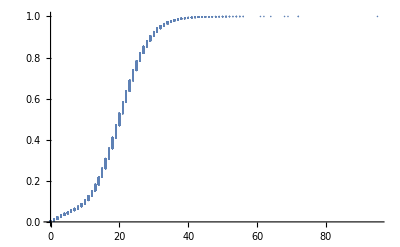

```mathematica
plotcdf=ListPlot[dataplotcdf, PlotRange->All]
```

## Fitting the CDF with a Gaussian Distribution CDF

From Wikipedia

-Graphics-

```mathematica
nlm=NonlinearModelFit[dataplotcdf, amp/2× (1+Erf[(x-μ)/(σ √2)]),{amp,μ,σ},x]
```

FittedModel[0.49996 (1+Erf[0.0981379 (-20.0122+x)])]

```mathematica
nlm["BestFitParameters"]
```

{amp→0.999921,μ→20.0122,σ→7.20524}

```mathematica
nlm["RSquared"]
```

0.999397

## Plotting the Fit of the CDF

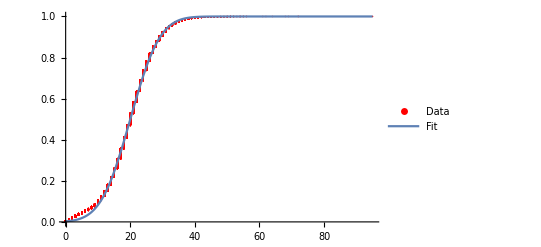

```mathematica
Show[ListPlot[dataplotcdf, PlotRange->All, PlotStyle->Red,PlotLegends->LineLegend[{"Data"}]],Plot[nlm[x],{x,0,Max[localization]},PlotLegends->LineLegend[{"Fit"}]]]
```

## Overlay Fitting Line with the Histogram (PDF)

```mathematica
datahistogram=Table[localization⟦i,1⟧,{i,Length[localization]}];
```

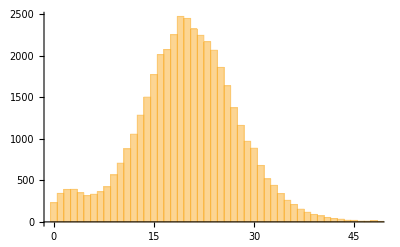

```mathematica
Histogram[{datahistogram},1000]
```

Gaussian PDF from Wikipedia

-Graphics-

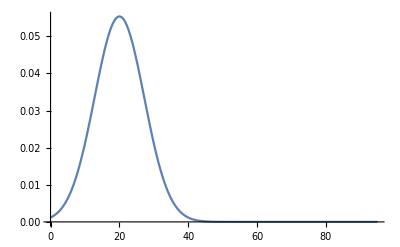

```mathematica
Plot[(nlm["BestFitParameters"]⟦1,2⟧)/(nlm["BestFitParameters"]⟦3,2⟧√(2π))Exp[-1/2((x-nlm["BestFitParameters"]⟦2,2⟧)/(nlm["BestFitParameters"]⟦3,2⟧))^2],{x,0,Max[localization]}, PlotRange->Full]
```

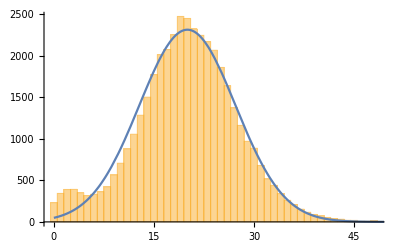

```mathematica
Show[Histogram[{datahistogram},1000],Plot[((5.5*7600)/(nlm["BestFitParameters"]⟦3,2⟧√(2π)))Exp[-(1/2)((x-nlm["BestFitParameters"]⟦2,2⟧)/nlm["BestFitParameters"]⟦3,2⟧)^2],{x,0,Max[localization]},PlotRange->All]]
```

```mathematica
ymax=(nlm["BestFitParameters"]⟦1,2⟧)/(nlm["BestFitParameters"]⟦3,2⟧√(2π))Exp[-1/2(0/(nlm["BestFitParameters"]⟦3,2⟧))^2]
```

0.055364

```mathematica
halfymax=ymax/2
```

0.027682

```mathematica
Solve[(nlm["BestFitParameters"]⟦1,2⟧)/(nlm["BestFitParameters"]⟦3,2⟧√(2π))Exp[-1/2((x-nlm["BestFitParameters"]⟦2,2⟧)/(nlm["BestFitParameters"]⟦3,2⟧))^2]==halfymax,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→11.5287},{x→28.4958}}

## Using MLE Estimation to Fit the Data

```mathematica
mle=EstimatedDistribution[datahistogram, NormalDistribution[α,β], ParameterEstimator->"MaximumLikelihood"]
```

NormalDistribution[19.8871,7.71963]

```mathematica
mle⟦1⟧
```

19.8871

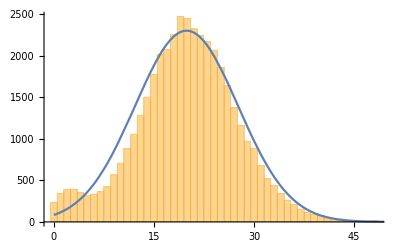

```mathematica
Show[Histogram[{datahistogram},320],Plot[((5.5*8100)/(mle⟦2⟧√(2π)))Exp[-(1/2)((x-mle⟦1⟧)/mle⟦2⟧)^2],{x,0,Max[localization]},PlotRange->All]]
```

```mathematica
ymaxmle=1/(mle⟦2⟧√(2π))Exp[-1/2(0/mle⟦2⟧)^2]
```

0.051679

```mathematica
halfymaxmle=ymaxmle/2
```

0.0258395

```mathematica
Solve[1/(mle⟦2⟧√(2π))Exp[-1/2((x-mle⟦1⟧)/mle⟦2⟧)^2]==halfymaxmle,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→10.7979},{x→28.9762}}

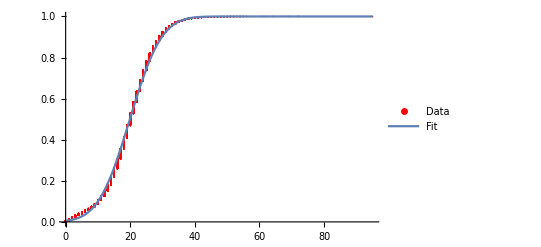

```mathematica
Show[ListPlot[dataplotcdf, PlotRange->All, PlotStyle->Red,PlotLegends->LineLegend[{"Data"}]],Plot[CDF[mle,x],{x,0,Max[localization]},PlotRange->All,PlotLegends->LineLegend[{"Fit"}]]]
```